```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
Dd[n_, z_] := Sum[ z^k/k! P[n,k],{k,0,Log[2,n]}]
Rd[n_] := Rd[n] = List@@NRoots[ Dd[n,x]==0,x][[All,2]]
Dp[n_, z_] := Product[1-z/k,{k,Rd[n]}]
```

```mathematica
Rd[100]
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
Sum[ -1/k,{k,Rd[100]}]
```

28.5333+0. ⅈ

```mathematica
Dp[100,1]
```

100.+1.77636×10^-15 ⅈ

```mathematica
Dp[100,2]
```

482.+2.84217×10^-14 ⅈ

```mathematica
Dp[100,3]
```

1471.+1.13687×10^-13 ⅈ

```mathematica
Dp[100,-1]
```

1.+2.77556×10^-17 ⅈ

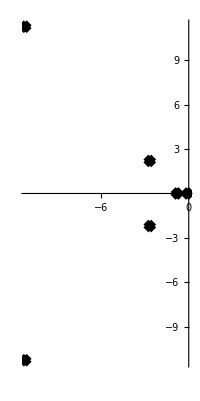

```mathematica
RootLocusPlot[1/Dd[96,x],{k,0,1}]
```